# An example needing EFFORT

### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

```mathematica
NotebookDirectory[]
```

C:\Users\cavin\OneDrive - southern.edu\Documents\SessieRepos\SSS-Experiments\KC\

```mathematica
ParentDirectory[NotebookDirectory[]]
```

C:\Users\cavin\OneDrive - southern.edu\Documents\SessieRepos\SSS-Experiments

### Test

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[6308190100]
```

<|Index→6308190100,QCode→34243232424233,RuleSet→{AB→BA,AA→B,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

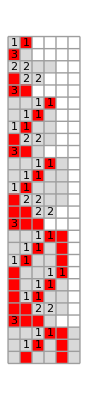



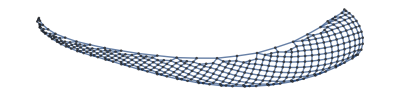
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "AB",800, (* choose an appropriate initial state string, and # steps *)
(* options *) Min->1,Max->400,SSSMin->Automatic,SSSMax->27,NetMin->Automatic,NetMax->384,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];(* options can be changed or omitted, but these are reasonable choices *)
```

Remember the buttons in SSSInteractiveDisplay to use the options you selected either one time or as default:

```mathematica
SSSInteractiveDisplay[sss01]
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,3→5,«1554»,796→797,797→798,796→798,795→799,748→799,755→800}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42},{44},{1,2,3},{1,3},{1,3},{3,45},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,4},{1,2},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.  I don’t believe anything after the last 44.

```mathematica
Position[nds01,44]
```

{{704,1},{708,2},{751,1}}

```mathematica
nds01[[1;;750]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42}}

Try the reduction:

```mathematica
rsl01=ReduceSetList[nds01[[1;;750]]]
```

{{1,3},{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,44},€^13[€^2[{1,3}],{3,42}],{1,51},{1,2},{1,42}}

Look for a most compressed part.  Nothing jumps out.  But from this point, I can easily finish the reduction manually.  Copy the result, add some extra lines (<Enter> key) to line up parts. We might use the near-repeated part  €_(n$1⊨1)^2[{??+2 (-1+n$1)}] for alignment:

```mathematica
{{1,3},
{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},
€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},
€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},
€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},
€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},
€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},
€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},
€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},
€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},
€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},
€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},
€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},
€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},
€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},
...}
```

Get an editable version of that last complete line:

```mathematica
rsl01[[-24;;-9]]
```

{€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40}}

```mathematica
rsl01[[-24;;-9]]//InputForm
```

{IndexedConcatenate[{39 + 2*(-1 + n$1)}, {n$1, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 41}, IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 39}, 12], {1, 48}, {1, 2}, {1, 39}, {41}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 42}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 40}, 12], {1, 4}, {1, 2}, {1, 40}}

```mathematica
{IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, k-1], {1, 4}, {1, 2}, {1, 3k+1}}/.k->13
```

{€_(j⊨1)^2[{39+2 (-1+j)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40}}

```mathematica
{IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, k-1], {1, 4}, {1, 2}, {1, 3k+1}}/.k->1
```

```mathematica
{€_(j⊨1)^2[{3+2 (-1+j)}],{1,2,3},€^2[{1,3}],{3,5},€^0[€^2[{1,3}],{3,3}],{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},€^0[€^2[{1,3}],{3,4}],{1,4},{1,2},{1,4}}
```

Most of those lines follow a clear pattern, this is working!  (I have no idea why the function ReduceSetLists wasn’t able to do the job for us: come back to this question later.)

Might this work with k starting earlier?  No, we can have a 0 (or less) as upper limit for an IC, but not anywhere else:

```mathematica
{IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, k-1], {1, 4}, {1, 2}, {1, 3k+1}}/.k->0
```

```mathematica
{€_(j⊨1)^2[{2 (-1+j)}],{1,2,3},€^2[{1,3}],{3,2},€^-1[€^2[{1,3}],{3,0}],{1,9},{1,2},{1,0},{2},{1,2,3},€^2[{1,3}],{3,3},€^-1[€^2[{1,3}],{3,1}],{1,4},{1,2},{1,1}}
```

```mathematica
Clear[k,j];  (* Now build our own! *)
rsl01IC={IndexedConcatenate[
IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, k-1], {1, 4}, {1, 2}, {1, 3k+1},
{k,1,13}]}
```

{€_(k⊨1)^13[€_(j⊨1)^2[{2 (-1+j)+3 k}],{1,2,3},€^2[{1,3}],{3,2+3 k},€^(-1+k)[€^2[{1,3}],{3,3 k}],{1,9+3 k},{1,2},{1,3 k},{2+3 k},{1,2,3},€^2[{1,3}],{3,3+3 k},€^(-1+k)[€^2[{1,3}],{3,1+3 k}],{1,4},{1,2},{1,1+3 k}]}

```mathematica
rsl01IC//ExpandAll //Short
```

{{3},{5},{1,2,3},{1,3},{1,3},{3,5},«677»,{1,3},{1,3},{3,40},{1,4},{1,2},{1,40}}

```mathematica
SequencePosition[nds01,{{3},{5},{1,2,3}}]
```

{{14,16}}

```mathematica
Length/@{nds01[[14;;]],rsl01IC//ExpandAll}
```

{784,689}

```mathematica
Length/@{nds01[[14;;689+14-1]],(ExpandAll@rsl01IC)}
```

{689,689}

```mathematica
Equal@@{nds01[[14;;689+14-1]],(ExpandAll@rsl01IC)}
```

True

I love it when a plan comes together!

```mathematica
Transpose@{nds01[[14;;689+14-1]],(ExpandAll@rsl01IC)}//Grid
```

{3} | {3}
{5} | {5}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,5} | {3,5}
{1,12} | {1,12}
{1,2} | {1,2}
{1,3} | {1,3}
{5} | {5}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,6} | {3,6}
{1,4} | {1,4}
{1,2} | {1,2}
{1,4} | {1,4}
{6} | {6}
{8} | {8}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,8} | {3,8}
{1,3} | {1,3}
{1,3} | {1,3}
{3,6} | {3,6}
{1,15} | {1,15}
{1,2} | {1,2}
{1,6} | {1,6}
{8} | {8}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,3} | {1,3}
{1,3} | {1,3}
{3,7} | {3,7}
{1,4} | {1,4}
{1,2} | {1,2}
{1,7} | {1,7}
{9} | {9}
{11} | {11}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,11} | {3,11}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,18} | {1,18}
{1,2} | {1,2}
{1,9} | {1,9}
{11} | {11}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,10} | {3,10}
{1,3} | {1,3}
{1,3} | {1,3}
{3,10} | {3,10}
{1,4} | {1,4}
{1,2} | {1,2}
{1,10} | {1,10}
{12} | {12}
{14} | {14}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,14} | {3,14}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,21} | {1,21}
{1,2} | {1,2}
{1,12} | {1,12}
{14} | {14}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,4} | {1,4}
{1,2} | {1,2}
{1,13} | {1,13}
{15} | {15}
{17} | {17}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,17} | {3,17}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,24} | {1,24}
{1,2} | {1,2}
{1,15} | {1,15}
{17} | {17}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,4} | {1,4}
{1,2} | {1,2}
{1,16} | {1,16}
{18} | {18}
{20} | {20}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,20} | {3,20}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,27} | {1,27}
{1,2} | {1,2}
{1,18} | {1,18}
{20} | {20}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,4} | {1,4}
{1,2} | {1,2}
{1,19} | {1,19}
{21} | {21}
{23} | {23}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,23} | {3,23}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,30} | {1,30}
{1,2} | {1,2}
{1,21} | {1,21}
{23} | {23}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,4} | {1,4}
{1,2} | {1,2}
{1,22} | {1,22}
{24} | {24}
{26} | {26}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,26} | {3,26}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,33} | {1,33}
{1,2} | {1,2}
{1,24} | {1,24}
{26} | {26}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,4} | {1,4}
{1,2} | {1,2}
{1,25} | {1,25}
{27} | {27}
{29} | {29}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,29} | {3,29}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,36} | {1,36}
{1,2} | {1,2}
{1,27} | {1,27}
{29} | {29}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,4} | {1,4}
{1,2} | {1,2}
{1,28} | {1,28}
{30} | {30}
{32} | {32}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,32} | {3,32}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,39} | {1,39}
{1,2} | {1,2}
{1,30} | {1,30}
{32} | {32}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,4} | {1,4}
{1,2} | {1,2}
{1,31} | {1,31}
{33} | {33}
{35} | {35}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,35} | {3,35}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,42} | {1,42}
{1,2} | {1,2}
{1,33} | {1,33}
{35} | {35}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,4} | {1,4}
{1,2} | {1,2}
{1,34} | {1,34}
{36} | {36}
{38} | {38}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,38} | {3,38}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,45} | {1,45}
{1,2} | {1,2}
{1,36} | {1,36}
{38} | {38}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,4} | {1,4}
{1,2} | {1,2}
{1,37} | {1,37}
{39} | {39}
{41} | {41}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,41} | {3,41}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,48} | {1,48}
{1,2} | {1,2}
{1,39} | {1,39}
{41} | {41}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,42} | {3,42}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,4} | {1,4}
{1,2} | {1,2}
{1,40} | {1,40}

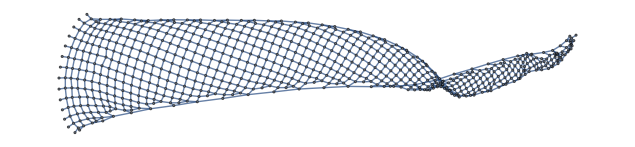

```mathematica
GraphPlot[FromNetDifferenceSets@ExpandAll@rsl01IC]
```

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->6308190100,"QCode"->"34243232424233","RuleSet"->{"AB"->"BA","AA"->"B","B"->"AAA"}|>
```

```mathematica
rsl01IC
```

```mathematica
{€_(k⊨1)^13[€_(j⊨1)^2[{3 k+2 (j-1)}],{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},
                             {3 k+2},{1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1}]}
```

```mathematica
{€_(k⊨1)^13[€_(j⊨1)^2[{3 k+2 (j-1)}],{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},
    €_(j⊨2)^2[{3 k+2 (j-1)}],{1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1}]}
```

```mathematica
ExpandAll[rsl01IC]
```

{{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40}}

### Why did ReduceSetList fail here?

Reminder: make window half-width now

```mathematica
$debug=True;
ReduceSetList[ExpandAll[rsl01IC]]
$debug=False;
```